## Making a list of all special symbols on arxiv.org

### Names of arXiv’s

Here we extract the names of the different arXiv categories from the names of the folders

```mathematica
SetDirectory[NotebookDirectory[]<>"Data\\9912"];
arXivNamesList=FileNames[];
```

### Extracting the Data Paths and File Names

We write a few functions to streamline the description of the data paths. We take Wolfram Alpha recognizable DateObjects as input and produce a list of filenames as the output.

```mathematica
currentDirectory =SetDirectory[NotebookDirectory[]];
dataPath = currentDirectory<>"\\Data";
yearMonthConvertor[yearmonthObject_]:=DateString[yearmonthObject,#]&/@{"YearShort","Month"};
allFilesinaMonth[yearmonthObject_,arXivType_]:=FileNames["*",dataPath<>"\\"<>(StringJoin@yearMonthConvertor[yearmonthObject])<>"\\"<>arXivType<>"\\*"];
allFileNames[startMonthObject_,endMonthObject_,arXivType_]:=Flatten[allFilesinaMonth[#,arXivType]&/@DateRange[startMonthObject,endMonthObject]];
```

Test our code here:

```mathematica
(* allFileNames[LinguisticAssistant,LinguisticAssistant,"astro-ph"]*)
```

### List of unwanted symbols

```mathematica
unwantedSymbols=FromCharacterCode/@{8201,8211,8217,8220,8221,8242,8243,8289,8290,8764,8805,8818};
```

### Symbols in an article

Given an arXiv document we find all the special characters in it and their frequencies

```mathematica
allSymbols[article_]:=KeyDrop[KeySelect[Counts[Characters[Import[article,"Text"]]],ToCharacterCode[#]⟦1⟧>168&],unwantedSymbols];
```

### Symbols in an arXiv category from start month to end month

Here we write functions to aggregate statistics of papers on the arXiv between any two months (within the range of arXiv’s existence), sorted in descending order by the number of occurrences of the symbol.

```mathematica
howManyAllSymbols[startMonthObject_,endMonthObject_,arXivType_]:=Sort[Merge[ParallelMap[allSymbols,allFileNames[startMonthObject,endMonthObject,arXivType]],Total],Greater];
howManyArticles[startMonthObject_,endMonthObject_,arXivType_]:=Length[allFileNames[startMonthObject,endMonthObject,arXivType]];
```

Below we work out the number of each symbol from January 1992 till December 2008.

```mathematica
howManyAllSymbols[DateObject[{1992,01}],DateObject[{2008,12}],"astro-ph"]
howManyArticles[DateObject[{1992,01}],DateObject[{2000,12}],"astro-ph"]
```

<|±→759731,α→503578,×→344826,μ→336542,σ→334054,ν→295981,γ→272671,Ω→249878,λ→244741,ρ→243121,δ→227166,β→223502,Δ→222873,⊙→216231,θ→207771,ϕ→183595,τ→183220,π→168966,≈→154344,∂→134358,˙→128944,χ→128773,η→128335,.af→127895,∘→125635,→→124818,Å→121725,ϵ→119528,—→114335,≤→113775,ω→109532,≃→106161,∫→99745,ξ→96902,…→96550,é→95086,Γ→92551,ℓ→92164,Λ→88067,⟩→87222,⟨→86969,⌃→78110,∝→72402,⋅→71323,≡→69318,κ→63778,‘→63021,∞→55360,†→55257,Φ→54721,ö→52286,∑→49749,ψ→47563,φ→44859,Σ→44162,ζ→39971,∇→39969,°→37627,í→37099,á→35501,ü→34027,≳→31578,☉→29552,ε→29216,≪→28631,⋆→26396,ó→26215,∗→24434,Ψ→24096,Θ→23571,≫→21600,⊥→20582,µ→19666,⁣→18972,ä→17997,∥→16305,ń→15265, →13501, →12729,≠→11704,Π→10982,∙→10940,è→10619,⋯→9319,¶→9115,ϑ→8659,ϖ→8449,ñ→8303,∈→7604,⊕→6707,ø→6424,ℏ→6318,ć→6050,Υ→5009,à→4766,∣→4628,ϱ→4085,ç→3681, →3627,ô→3364,υ→3309,Č→2849,ł→2845,Ö→2738,△→2710,ß→2668,Ξ→2631,∓→2598,ê→2289,ź→2278,.b4→2276,ℜ→2252,≅→2202,⊥→2112,⟶→2099,∏→2081, →2010,ã→1928,↔→1917,ú→1791,î→1780,ι→1723,□→1690,É→1606,‡→1601,ı→1555,æ→1523,ż→1474,√→1379,Ê→1312,⊗→1297,⇒→1273,Ż→1262,↑→1247,č→1099,↓→1095,å→1047,Ł→998,š→934,∧→891,⩽→889,ò→860,÷→827,∩→822,Ø→795,✓→777,Ž→730,ý→727,â→693,ï→653,ℑ→634,∮→561,⋮→554,Ć→549,∀→512,⇌→506,ς→497,Á→490,©→489,Ð→485,ş→481,←→481,ⅆ→478,⊤→471,˘→466,ù→448,̆→443,ğ→440,↦→410,⩾→406,ž→406,⋄→393,̃→381,Ṁ→380,ë→376,Ã→373,⊂→366,℘→362,Ü→358,▽→341,○→337,Š→334,ℵ→299,⇔→298,⟹→285,∎→282,̧→271,⏟→255,∪→244,ϰ→237,ő→228,ì→222,ū→219,∅→215,ř→205,́→199,⊡→197,ė→194,⋱→193,ȩ→188,♭→173,♯→167,ō→158,⟺→158,Ó→155,∖→153,⟷→152,ś→148,≐→147,û→147,İ→142,õ→141,ĭ→140,̱→132,→130,œ→129,⏞→128,◇→128,ⅇ→124,Â→115,ǹ→114,∬→108,⊔→108,∉→101,≻→96,̀→92,■→90,̈→90,Ô→88,⊘→87,⌊→85,↘→85,.bc→82,⌋→81,̇→80,ǧ→78,̄→77,∪→76,♢→75,Ṗ→72,Ç→71,▲→70,∨→68,∠→68,⊓→66,Õ→65,Ò→63,ŕ→61,⪅→59,♮→58,ṁ→58,⟼→58,Ė→55,∃→53,≿→51,ň→51,≘→51,̋→50,⊖→47,⊚→46,À→46,♠→45,∽→44,≦→44,♡→43,⇄→42,≌→40,≍→40,↗→40,Ś→40,⪆→39,⃗→37,−→37,ű→37,≶→37,Î→36,∋→36,̂→36,ⅈ→35,≺→35,⇀→34,ÿ→32,↖→31,↙→31,♣→31,⇓→31,Ş→31,∄→30,⃝→30,⇑→30,⊆→29,◆→29,␣→28,ě→28,⪝→28,.bd→28,̊→27,ṟ→27,¬→27,▼→26,ỳ→26,ũ→26,⌉→25,Ñ→25,͡→25,ā→23,Œ→22,®→22,.b3→22,⅓→22,Ȧ→22,≊→21,Ṫ→21,ℕ→20,ĉ→20,Ú→20,∩→20,⊃→20,★→19,⌈→19,⟵→19,•→18,.aa→18,⇆→18,∐→18,≜→17,⊞→17,⊢→17,ℝ→17,Ĉ→17,⪎→17,≷→16,Ź→16,Æ→16,Ý→15,ẽ→15,▷→14,≧→14,Ä→14,ǵ→14,ǔ→13,ĝ→13,ḿ→13,⇐→13,⪍→13,È→13,≗→12,Ā→12,ȧ→12,̌→12,¸→11,⃡→11,ḧ→11,↼→10,⇁→10,¿→10,◁→10,⇋→10,Ẽ→10,⌀→10,ĺ→10,ī→10,⪞→10,ţ→10,⋉→9,Í→9,ṽ→8,ẹ→8,╱→8,⪰→8,Ḋ→8,Ū→8,™→7,Ř→7,«→7,Ľ→7,∭→7,≀→7,ǎ→7,ǒ→7,ẗ→7,̣→7,.b2→7,Ń→7,˝→7,ă→7,⅔→7,ǐ→7,≂→6,⋘→6,№→6,Ṣ→6,↛→6,ṕ→6,.ba→6,Ẇ→6,⊳→6,ṫ→6,ŭ→6,ē→5,⋙→5,ϝ→5,Ṙ→5,↪→5,.b9→5,≢→5,Ï→5,ĕ→5,ṣ→5,Ĩ→5,⊲→5,↕→5,ŝ→4,ṗ→4,⌢→4,ℷ→4,ℂ→4,·→4,ṡ→4,⟸→4,⊧→4,ẑ→4,ŵ→3,⟧→3,⟦→3,ṅ→3,∴→3,↩→3,Ĥ→3,ḟ→3,≉→3,Ẑ→3,ℤ→3,Ṕ→3,ȯ→3,Ḣ→3,⪖→3,⇕→3,ḃ→3,Ṅ→3,.be→3,Ṡ→3,➮→2,➭→2,➯→2,➬→2,◀→2,Ì→2,ċ→2,ẇ→2,ℶ→2,⨌→2,▶→2,⊛→2,ĩ→2,≯→2,Ĺ→2,Þ→2,↝→2,⪯→2,Ë→2,Ḟ→2,⋀→2,ẏ→2,Ṟ→2,ŷ→2,ẃ→2,ḳ→2,℧→2,ṯ→1,⇈→1,Ŝ→1,⊀→1,↣→1,Ğ→1,≮→1,∦→1,╲→1,Ŕ→1,ġ→1,Ṛ→1,⌣→1,Ţ→1,ð→1,⊇→1,Û→1,⋁→1,ḋ→1,ť→1,⪋→1,ę→1,ḏ→1,Ḧ→1,⪕→1,✵→1,Ṭ→1,⊄→1,þ→1,Ũ→1,Ō→1,Ő→1,»→1|>

```mathematica
WordCloud[<|"±"->759731,"α"->503578,"×"->344826,"μ"->336542,"σ"->334054,"ν"->295981,"γ"->272671,"Ω"->249878,"λ"->244741,"ρ"->243121,"δ"->227166,"β"->223502,"Δ"->222873,"⊙"->216231,"θ"->207771,"ϕ"->183595,"τ"->183220,"π"->168966,"≈"->154344,"∂"->134358,"˙"->128944,"χ"->128773,"η"->128335,".af"->127895,"∘"->125635,"→"->124818,"Å"->121725,"ϵ"->119528,"—"->114335,"≤"->113775,"ω"->109532,"≃"->106161,"∫"->99745,"ξ"->96902,"…"->96550,"é"->95086,"Γ"->92551,"ℓ"->92164,"Λ"->88067,"⟩"->87222,"⟨"->86969,"⌃"->78110,"∝"->72402,"⋅"->71323,"≡"->69318,"κ"->63778,"‘"->63021,"∞"->55360,"†"->55257,"Φ"->54721,"ö"->52286,"∑"->49749,"ψ"->47563,"φ"->44859,"Σ"->44162,"ζ"->39971,"∇"->39969,"°"->37627,"í"->37099,"á"->35501,"ü"->34027,"≳"->31578,"☉"->29552,"ε"->29216,"≪"->28631,"⋆"->26396,"ó"->26215,"∗"->24434,"Ψ"->24096,"Θ"->23571,"≫"->21600,"⊥"->20582,"µ"->19666,"⁣"->18972,"ä"->17997,"∥"->16305,"ń"->15265," "->13501," "->12729,"≠"->11704,"Π"->10982,"∙"->10940,"è"->10619,"⋯"->9319,"¶"->9115,"ϑ"->8659,"ϖ"->8449,"ñ"->8303,"∈"->7604,"⊕"->6707,"ø"->6424,"ℏ"->6318,"ć"->6050,"Υ"->5009,"à"->4766,"∣"->4628,"ϱ"->4085,"ç"->3681," "->3627,"ô"->3364,"υ"->3309,"Č"->2849,"ł"->2845,"Ö"->2738,"△"->2710,"ß"->2668,"Ξ"->2631,"∓"->2598,"ê"->2289,"ź"->2278,".b4"->2276,"ℜ"->2252,"≅"->2202,"⊥"->2112,"⟶"->2099,"∏"->2081," "->2010,"ã"->1928,"↔"->1917,"ú"->1791,"î"->1780,"ι"->1723,"□"->1690,"É"->1606,"‡"->1601,"ı"->1555,"æ"->1523,"ż"->1474,"√"->1379,"Ê"->1312,"⊗"->1297,"⇒"->1273,"Ż"->1262,"↑"->1247,"č"->1099,"↓"->1095,"å"->1047,"Ł"->998,"š"->934,"∧"->891,"⩽"->889,"ò"->860,"÷"->827,"∩"->822,"Ø"->795,"✓"->777,"Ž"->730,"ý"->727,"â"->693,"ï"->653,"ℑ"->634,"∮"->561,"⋮"->554,"Ć"->549,"∀"->512,"⇌"->506,"ς"->497,"Á"->490,"©"->489,"Ð"->485,"ş"->481,"←"->481,"ⅆ"->478,"⊤"->471,"˘"->466,"ù"->448,"̆"->443,"ğ"->440,"↦"->410,"⩾"->406,"ž"->406,"⋄"->393,"̃"->381,"Ṁ"->380,"ë"->376,"Ã"->373,"⊂"->366,"℘"->362,"Ü"->358,"▽"->341,"○"->337,"Š"->334,"ℵ"->299,"⇔"->298,"⟹"->285,"∎"->282,"̧"->271,"⏟"->255,"∪"->244,"ϰ"->237,"ő"->228,"ì"->222,"ū"->219,"∅"->215,"ř"->205,"́"->199,"⊡"->197,"ė"->194,"⋱"->193,"ȩ"->188,"♭"->173,"♯"->167,"ō"->158,"⟺"->158,"Ó"->155,"∖"->153,"⟷"->152,"ś"->148,"≐"->147,"û"->147,"İ"->142,"õ"->141,"ĭ"->140,"̱"->132,""->130,"œ"->129,"⏞"->128,"◇"->128,"ⅇ"->124,"Â"->115,"ǹ"->114,"∬"->108,"⊔"->108,"∉"->101,"≻"->96,"̀"->92,"■"->90,"̈"->90,"Ô"->88,"⊘"->87,"⌊"->85,"↘"->85,".bc"->82,"⌋"->81,"̇"->80,"ǧ"->78,"̄"->77,"∪"->76,"♢"->75,"Ṗ"->72,"Ç"->71,"▲"->70,"∨"->68,"∠"->68,"⊓"->66,"Õ"->65,"Ò"->63,"ŕ"->61,"⪅"->59,"♮"->58,"ṁ"->58,"⟼"->58,"Ė"->55,"∃"->53,"≿"->51,"ň"->51,"≘"->51,"̋"->50,"⊖"->47,"⊚"->46,"À"->46,"♠"->45,"∽"->44,"≦"->44,"♡"->43,"⇄"->42,"≌"->40,"≍"->40,"↗"->40,"Ś"->40,"⪆"->39,"⃗"->37,"−"->37,"ű"->37,"≶"->37,"Î"->36,"∋"->36,"̂"->36,"ⅈ"->35,"≺"->35,"⇀"->34,"ÿ"->32,"↖"->31,"↙"->31,"♣"->31,"⇓"->31,"Ş"->31,"∄"->30,"⃝"->30,"⇑"->30,"⊆"->29,"◆"->29,"␣"->28,"ě"->28,"⪝"->28,".bd"->28,"̊"->27,"ṟ"->27,"¬"->27,"▼"->26,"ỳ"->26,"ũ"->26,"⌉"->25,"Ñ"->25,"͡"->25,"ā"->23,"Œ"->22,"®"->22,".b3"->22,"⅓"->22,"Ȧ"->22,"≊"->21,"Ṫ"->21,"ℕ"->20,"ĉ"->20,"Ú"->20,"∩"->20,"⊃"->20,"★"->19,"⌈"->19,"⟵"->19,"•"->18,".aa"->18,"⇆"->18,"∐"->18,"≜"->17,"⊞"->17,"⊢"->17,"ℝ"->17,"Ĉ"->17,"⪎"->17,"≷"->16,"Ź"->16,"Æ"->16,"Ý"->15,"ẽ"->15,"▷"->14,"≧"->14,"Ä"->14,"ǵ"->14,"ǔ"->13,"ĝ"->13,"ḿ"->13,"⇐"->13,"⪍"->13,"È"->13,"≗"->12,"Ā"->12,"ȧ"->12,"̌"->12,"¸"->11,"⃡"->11,"ḧ"->11,"↼"->10,"⇁"->10,"¿"->10,"◁"->10,"⇋"->10,"Ẽ"->10,"⌀"->10,"ĺ"->10,"ī"->10,"⪞"->10,"ţ"->10,"⋉"->9,"Í"->9,"ṽ"->8,"ẹ"->8,"╱"->8,"⪰"->8,"Ḋ"->8,"Ū"->8,"™"->7,"Ř"->7,"«"->7,"Ľ"->7,"∭"->7,"≀"->7,"ǎ"->7,"ǒ"->7,"ẗ"->7,"̣"->7,".b2"->7,"Ń"->7,"˝"->7,"ă"->7,"⅔"->7,"ǐ"->7,"≂"->6,"⋘"->6,"№"->6,"Ṣ"->6,"↛"->6,"ṕ"->6,".ba"->6,"Ẇ"->6,"⊳"->6,"ṫ"->6,"ŭ"->6,"ē"->5,"⋙"->5,"ϝ"->5,"Ṙ"->5,"↪"->5,".b9"->5,"≢"->5,"Ï"->5,"ĕ"->5,"ṣ"->5,"Ĩ"->5,"⊲"->5,"↕"->5,"ŝ"->4,"ṗ"->4,"⌢"->4,"ℷ"->4,"ℂ"->4,"·"->4,"ṡ"->4,"⟸"->4,"⊧"->4,"ẑ"->4,"ŵ"->3,"⟧"->3,"⟦"->3,"ṅ"->3,"∴"->3,"↩"->3,"Ĥ"->3,"ḟ"->3,"≉"->3,"Ẑ"->3,"ℤ"->3,"Ṕ"->3,"ȯ"->3,"Ḣ"->3,"⪖"->3,"⇕"->3,"ḃ"->3,"Ṅ"->3,".be"->3,"Ṡ"->3,"➮"->2,"➭"->2,"➯"->2,"➬"->2,"◀"->2,"Ì"->2,"ċ"->2,"ẇ"->2,"ℶ"->2,"⨌"->2,"▶"->2,"⊛"->2,"ĩ"->2,"≯"->2,"Ĺ"->2,"Þ"->2,"↝"->2,"⪯"->2,"Ë"->2,"Ḟ"->2,"⋀"->2,"ẏ"->2,"Ṟ"->2,"ŷ"->2,"ẃ"->2,"ḳ"->2,"℧"->2,"ṯ"->1,"⇈"->1,"Ŝ"->1,"⊀"->1,"↣"->1,"Ğ"->1,"≮"->1,"∦"->1,"╲"->1,"Ŕ"->1,"ġ"->1,"Ṛ"->1,"⌣"->1,"Ţ"->1,"ð"->1,"⊇"->1,"Û"->1,"⋁"->1,"ḋ"->1,"ť"->1,"⪋"->1,"ę"->1,"ḏ"->1,"Ḧ"->1,"⪕"->1,"✵"->1,"Ṭ"->1,"⊄"->1,"þ"->1,"Ũ"->1,"Ō"->1,"Ő"->1,"»"->1|>]
```

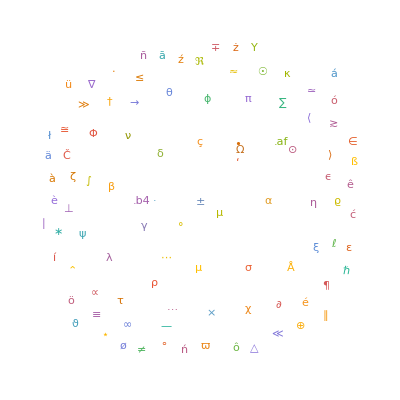
```mathematica
Export["C:\\Users\\bhujyo\\Documents\\Wolfram Mathematica\\Work Done\\Project\\MyProject\\output\\astrophWC.jpg",-Graphics-]
```

C:\Users\bhujyo\Documents\Wolfram Mathematica\Work Done\Project\MyProject\output\astrophWC.jpg

```mathematica
(*Export["C:\\Users\\bhujyo\\Documents\\Wolfram Mathematica\\Work Done\\Project\\MyProject\\output\\AllSymbols.txt",%49]*)
```

C:\Users\bhujyo\Documents\Wolfram Mathematica\Work Done\Project\MyProject\output\AllSymbols.txt

### Most Used

What is the most used symbol between two months

```mathematica
mostUsedinPeriod[startmonthObject_,endmonthObject_,arXivType_,normalize_:1]/;howManyArticles[startmonthObject,endmonthObject,arXivType]≠0:=TakeLargest[howManyAllSymbols[startmonthObject,endmonthObject,arXivType]/howManyArticles[startmonthObject,endmonthObject,arXivType]^normalize//N,1];
mostUsedinMonth[monthObject_,arXivType_,normalize_:1]:=mostUsedinPeriod[monthObject,monthObject,arXivType,normalize];
mostUsedinYear[year_,arXivType_,normalize_:1]:=mostUsedinPeriod[DateObject[{year,1}],DateObject[{year,12}],arXivType,normalize];
```

Example from June 2002 to May 2003 on hep-ph

```mathematica
mostUsedinPeriod[DateObject[{2002,6}],DateObject[{2003,5}],"hep-ph"]
```

<|μ→33.2548|>

```mathematica
mostUsedinMonth[DateObject[{1999, 6}],"hep-ph"]
```

<|μ→35.5663|>

```mathematica
mostUsedinYear[1998,"hep-ph"]
```

<|μ→34.7643|>

### Frequency Plots

```mathematica
symbolFrequencyPlot[startMonthObject_,endMonthObject_,arXivType_,symbol_]:=DateListStepPlot[{#,Module[{numberofArticles=howManyArticles[#,#,arXivType]},If[numberofArticles==0,0,(howManyAllSymbols[#,#,arXivType][symbol])/numberofArticles]]}&/@DateRange[startMonthObject,endMonthObject],PlotRange->{All,{0,All}}];
```

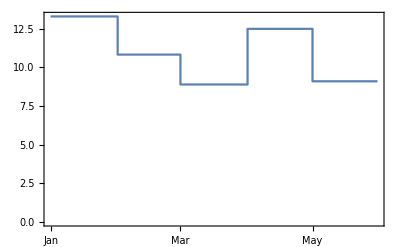

```mathematica
symbolFrequencyPlot[LinguisticAssistant,LinguisticAssistant,"astro-ph","α"]
```